```mathematica
Clear["Global`*"]
```

# Island-mainland matching alleles coevolution with two-patch model

```mathematica
WH[1,t_]:=pP[t](1-V) +(1-pP[t])S +(1-pP[t])(1-S)(1-V)
WH[2,t_]:=(1-pP[t])(1-V)+pP[t]S +pP[t](1-S)(1-V) 
WP[1,t_]:=pH[t]+(1-pH[t])(1-S)
WP[2,t_]:=(1-pH[t])+pH[t](1-S)
```

```mathematica
pH1[t_]:=(pH[t] WH[1,t])/(pH[t]WH[1,t]+(1-pH[t])WH[2,t])
pP1[t_]:=(pP[t] WP[1,t])/(pP[t]WP[1,t]+(1-pP[t])WP[2,t])
```

```mathematica
pH2[t_]:=pH1[t](1-mH )+mH/2
pP2[t_]:=pP1[t](1-mP)+mP/2
```

### Numerical time series

```mathematica
inits1={i1-> 0.495,i2-> 0.5,i3-> 0.5,i4-> 0.5};
pars1={p1-> 0.4117647058823529,p2-> 0.2200911052505395,p3-> 0.01,p4-> 0.01};
pars2={p1-> 0.3939393939393939,p2-> 0.4368677407268642,p3->0.01,p4-> 0.01};
pars3={p1-> 0.37500000000000006,p2-> 0.9004329004329,p3-> 0.01,p4-> 0.01};
```

```mathematica
Clear[timeSeries]
timeSeries[pars_,inits_,tmax_]:=timeSeries[pars,inits,tmax]=Block[
{WH,WP,pH1,pP1,pH2,pP2,S,V,mH,mP,pP,pH,i1,i2,i3,i4,p1,p2,p3,p4,out},

S=p1/.pars;
V=p2/.pars;
mH=p3/.pars;
mP=p4/.pars;

WH[1,t_]:=pP[t](1-V) +(1-pP[t])S +(1-pP[t])(1-S)(1-V);
WH[2,t_]:=(1-pP[t])(1-V)+pP[t]S +pP[t](1-S)(1-V) ;
WP[1,t_]:=pH[t]+(1-pH[t])(1-S);
WP[2,t_]:=(1-pH[t])+pH[t](1-S);

pH1[t_]:=(pH[t] WH[1,t])/(pH[t]WH[1,t]+(1-pH[t])WH[2,t]);
pP1[t_]:=(pP[t] WP[1,t])/(pP[t]WP[1,t]+(1-pP[t])WP[2,t]);

pH2[t_]:=pH1[t](1-mH )+mH/2;
pP2[t_]:=pP1[t](1-mP)+mP/2;

pH[t_]:=pH[t]=pH2[t-1];
pP[t_]:=pP[t]=pP2[t-1];

pH[0]=i1/.inits;
pP[0]=i2/.inits;

out={Table[j,{j,0,tmax}],
Table[pH[j],{j,0,tmax}],
Table[pP[j],{j,0,tmax}]}
]
```

```mathematica
maxT=1000;
```

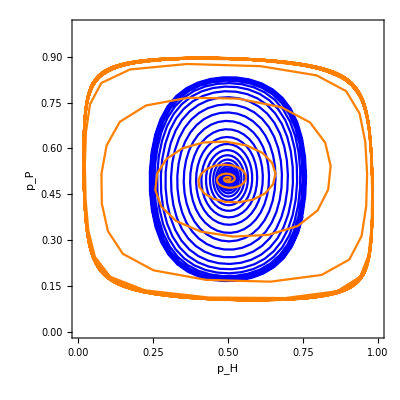

```mathematica
g=Show[ListLinePlot[Partition[Riffle[timeSeries[pars1,inits1,maxT][[2]],timeSeries[pars1,inits1,maxT][[3]]],2],PlotRange-> {{0,1},{0,1}},PlotStyle-> Red],
ListLinePlot[Partition[Riffle[timeSeries[pars2,inits1,maxT][[2]],timeSeries[pars2,inits1,maxT][[3]]],2],PlotRange-> {{0,1},{0,1}},PlotStyle-> Blue],ListLinePlot[Partition[Riffle[timeSeries[pars3,inits1,maxT][[2]],timeSeries[pars3,inits1,maxT][[3]]],2], PlotStyle-> Orange,PlotRange-> {{0,1},{0,1}}],Frame->  True,FrameLabel-> {"p_H","p_P"},AspectRatio-> 1]
```

```mathematica
Export["~/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/IslandMainland_Discrete_Phase.png",g,ImageResolution-> 300]
```

~/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/IslandMainland_Discrete_Phase.png

### Equilibria

```mathematica
equs={pH2[t],pP2[t]};
```

```mathematica
equs3=Map[Simplify[Series[#/.{mH->ϵ μH,mP->ϵ μP},{ϵ,0,2}],Assumptions->{S>0,V>0,μH>0,μP>0,ϵ>0}]&,equs];
```

```mathematica
equi=Solve[equs3=={pH[t],pP[t]},{pH[t],pP[t]}]
```

{{pH[t]→1/2,pP[t]→1/2}}

### Stability

```mathematica
JMtrx={
{D[pH2[t],pH[t]],D[pH2[t],pP[t]]},
{D[pP2[t],pH[t]],D[pP2[t],pP[t]]}};
```

```mathematica
Clear[JMtrxEqui,λList]
JMtrxEqui[e_]:=JMtrx/.equi[[e]]//Simplify;
λList[e_]:=JMtrxEqui[e]//Eigenvalues//FullSimplify;
```

#### Equilibrium 1 – polymorphic

```mathematica
JMtrxEqui[1]//MatrixForm
```

(1-mH | ((-1+mH) S V)/(2+(-2+S) V)
((-1+mP) S)/(-2+S) | 1-mP)

```mathematica
λList[1]
```

{-1/(2 (-2+S) (2+(-2+S) V))(4 (-2+mH+mP) (-1+V)+(-2+mH+mP) S^2 V-2 (-2+mH+mP) S (-1+2 V)+√(-2+S) √(2+(-2+S) V) √(2 (mH-mP)^2 (-2+S)+(4 (mH-mP)^2-4 (mH-mP)^2 S+(-2+mH+mP)^2 S^2) V)),1/(2 (-2+S) (2+(-2+S) V))(-4 (-2+mH+mP) (-1+V)-(-2+mH+mP) S^2 V+2 (-2+mH+mP) S (-1+2 V)+√(-2+S) √(2+(-2+S) V) √(2 (mH-mP)^2 (-2+S)+(4 (mH-mP)^2-4 (mH-mP)^2 S+(-2+mH+mP)^2 S^2) V))}

```mathematica
FullSimplify[√(-2+S) √(2+(-2+S) V) √(2 (mH-mP)^2 (-2+S)+(4 (mH-mP)^2-4 (mH-mP)^2 S+(-2+mH+mP)^2 S^2) V),Assumptions->{mH>0,mP>0,1>S>0,0<V<1}]
```

√((-2+S) (2+(-2+S) V)) √(2 (mH-mP)^2 (-2+S)+(4 (mH-mP)^2-4 (mH-mP)^2 S+(-2+mH+mP)^2 S^2) V)

```mathematica
Map[Simplify[#,Assumptions->{mH>0,mP>0,1>S>0,0<V<1}]&,λList[1][[1]]]
```

-1/(2 (-2+S) (2+(-2+S) V))(4 (-2+mH+mP) (-1+V)+(-2+mH+mP) S^2 V-2 (-2+mH+mP) S (-1+2 V)+√((-2+S) (2+(-2+S) V)) √(2 (mH-mP)^2 (-2+S)+(4 (mH-mP)^2-4 (mH-mP)^2 S+(-2+mH+mP)^2 S^2) V))

```mathematica
-1/(2 (-2+S) (2+(-2+S) V))(4 (-2+mH+mP) (-1+V)+(-2+mH+mP) S^2 V-2 (-2+mH+mP) S (-1+2 V))//FullSimplify
```

1/2 (2-mH-mP)

```mathematica
re=Re[λList[1][[1]]/.{S->0.1,V->0.3,mH->0,mP->0}]
im=Im[λList[1][[1]]/.{S->0.1,V->0.3,mH->0,mP->0}];
Sqrt[re^2+im^2];

re=Re[λList[1][[1]]/.{S->0.3,V->0.3,mH->0.001,mP->0.001}]
im=Im[λList[1][[1]]/.{S->0.3,V->0.3,mH->0.001,mP->0.001}]
Sqrt[re^2+im^2]
```

1.

0.999

0.103141

1.00431

Stable.

### Individual-Based Simulations

```mathematica
parsN={S-> 0,V->0.2,mH->0.05,mP->0.05,κH->300,κP->300,tMax->200};
parsN3={S-> 0,V->0.5,mH->0.05,mP->0.05,κH->300,κP->300,tMax->200};
parsN4={S-> 0,V->0.2,mH->0.01,mP->0.01,κH->300,κP->300,tMax->200};
parsN5={S-> 0,V->0.2,mH->0.001,mP->0.001,κH->300,κP->300,tMax->200};
pars1={S-> 0.8,V->0.2,a->0.1,mH->0.05,mP->0.05,κH->300,κP->300,tMax->200};
pars2={S->0.65,V->0.2,a->0.1,mH->0.05,mP->0.05,κH->300,κP->300,tMax->200};
pars3={S->0.8,V->0.5,a->0.1,mH->0.05,mP->0.05,κH->300,κP->300,tMax->200};
pars4={S->0.8,V->0.2,a->0.1,mH->0.01,mP->0.01,κH->300,κP->300,tMax->200};
pars5={S->0.8,V->0.2,a->0.1,mH->0.001,mP->0.001,κH->300,κP->300,tMax->200};
```

Absolute fitness values

```mathematica
Clear[WH]
WH[1,pVec_]:=pVec[[2]](1-V) +(1-pVec[[2]])S +(1-pVec[[2]])(1-S)(1-V);
WH[2,pVec_]:=(1-pVec[[2]])(1-V)+pVec[[2]]S +pVec[[2]](1-S)(1-V)  ;
WP[1,pVec_]:=pVec[[1]]+(1-pVec[[1]])(1-S);
WP[2,pVec_]:=(1-pVec[[1]])+pVec[[1]](1-S);
```

Relative fitness values

```mathematica
Clear[wH]
wH[pVec_]:=WH[1,pVec]/(pVec[[1]] WH[1,pVec]+(1-pVec[[1]])WH[2,pVec]) ;
wP[pVec_]:=WP[1,pVec]/(pVec[[2]] WP[1,pVec]+(1-pVec[[2]])WP[2,pVec]) ;
```

```mathematica
Clear[Sim2]
Sim2[pars_,intS_]:=Sim2[pars,intS]=Block[{out,g,nH1s,nP1s,nH2s,nP2s,nMH1,nMH2,nMP1,nMP2,nMH11,nMH12,nMH21,nMH22,nMP11,nMP12,nMP21,nMP22,nH1sm,nH2sm,nP1sm,nP2sm,nH11sm,nH21sm,nH12sm,nH22sm,nP11sm,nP12sm,nP21sm,nP22sm,nH1prime,nH2prime,nP1prime,nP2prime},out={{1/2,1/2}}//N;
For[g=1,g≤(tMax/.pars),g++,

(*Selection*)
nH1s=RandomVariate[BinomialDistribution[(κH/.pars),wH[out[[-1]]]out[[-1,1]]/.pars]];
nP1s=RandomVariate[BinomialDistribution[(κP/.pars),wP[out[[-1]]]out[[-1,2]]/.pars]];

(*Number of type 1 host migrants out of population 1*)
nMH11=RandomVariate[BinomialDistribution[nH1s,mH/.pars]];

(*Number of type 2 host migrants out of population 1*)
nMH12=RandomVariate[BinomialDistribution[κH-nH1s/.pars,mH/.pars]];

(*Number of type 1 hosts after migration*)
nH11sm=nH1s-nMH11+RandomVariate[BinomialDistribution[nMH11,0.5]]+RandomVariate[BinomialDistribution[nMH12,0.5]];

(*Number of type 1 parasite migrants out of populations 1 and 2*)
nMP11=RandomVariate[BinomialDistribution[nP1s,mP/.pars]];

(*Number of type 2 parasite migrants out of populations 1 and 2*)
nMP12=RandomVariate[BinomialDistribution[κP-nP1s/.pars,mP/.pars]];

(*Number of type 1 and type 2 hosts after migration for populations 1 and 2*)
nP11sm=nP1s-nMP11+RandomVariate[BinomialDistribution[nMP11,0.5]]+RandomVariate[BinomialDistribution[nMP12,0.5]];

AppendTo[out,{nH11sm/κH,nP11sm/κP}/.pars//N]
];
out
]
```

```mathematica
Clear[mean]
mean[pars_]:=mean[pars]=Mean[Table[2 Sim2[pars,j][[;;,1]](1-Sim2[pars,j][[;;,1]]),{j,1,2000}]]
```

```mathematica
Clear[SD]
SD[pars_]:=SD[pars]=Mean[Table[(2 Sim2[pars,j][[;;,1]](1-Sim2[pars,j][[;;,1]])-mean[pars])^2,{j,1,2000}]]//Sqrt;
```

```mathematica
leg2=LineLegend[{Directive[Blue,Opacity[0.2],Dashed],Directive[Blue,Opacity[0.4]],Directive[Blue]},{"Neutral","Coevolutionary, S=0.65","Coevolutionary, S=0.8"}]
```

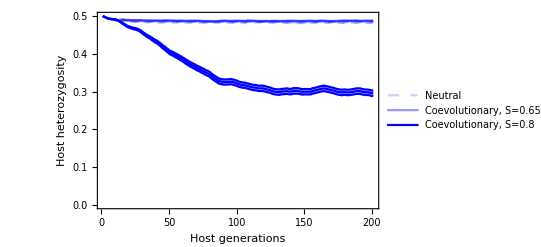

```mathematica
g1=Show[
ListLinePlot[{mean[parsN],mean[parsN]+(2SD[parsN])/Sqrt[2000],mean[parsN]-(2SD[parsN])/Sqrt[2000]},PlotStyle->Directive[Blue,Opacity[0.2],Dashed],Filling->{2->{{3},{Directive[Blue,Opacity[0.1]]}}}],
ListLinePlot[{mean[pars2],mean[pars2]+(2SD[pars2])/Sqrt[2000],mean[pars2]-(2SD[pars2])/Sqrt[2000]},PlotStyle->Directive[Blue,Opacity[0.4]],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],
ListLinePlot[{mean[pars1],mean[pars1]+(2SD[pars1])/Sqrt[2000],mean[pars1]-(2SD[pars1])/Sqrt[2000]},PlotStyle->Directive[Blue],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],
PlotRange-> {0,0.5},Frame->True,FrameLabel-> {"Host generations","Host heterozygosity"},Axes-> False];
g1Legend=Legended[g1,leg2]
```

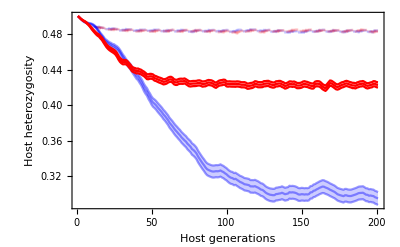

```mathematica
leg3=LineLegend[{Directive[Blue,Opacity[0.2],Dashed],Directive[Red,Opacity[0.2],Dashed],Directive[Blue],Directive[Red]},{"Neutral, V=0.2","Neutral, V=0.5","Coevolutionary, V=0.2","Coevolutionary, V=0.5"}]
g2=Show[
ListLinePlot[{mean[parsN],mean[parsN]+(2SD[parsN])/Sqrt[2000],mean[parsN]-(2SD[parsN])/Sqrt[2000]},PlotStyle->Directive[Blue,Opacity[0.2],Dashed],Filling->{2->{{3},{Directive[Blue,Opacity[0.1]]}}}],
ListLinePlot[{mean[parsN3],mean[parsN3]+(2SD[parsN3])/Sqrt[2000],mean[parsN3]-(2SD[parsN3])/Sqrt[2000]},PlotStyle->Directive[Red,Opacity[0.2],Dashed],Filling->{2->{{3},{Directive[Red,Opacity[0.1]]}}}],

ListLinePlot[{mean[pars1],mean[pars1]+(2SD[pars1])/Sqrt[2000],mean[pars1]-(2SD[pars1])/Sqrt[2000]},PlotStyle->Directive[Blue,Opacity[0.4]],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],
ListLinePlot[{mean[pars3],mean[pars3]+(2SD[pars3])/Sqrt[2000],mean[pars3]-(2SD[pars3])/Sqrt[2000]},PlotStyle->Directive[Red],Filling->{2->{{3},{Directive[Red,Opacity[0.2]]}}},PlotRange-> All],
PlotRange-> All,Frame->True,FrameLabel-> {"Host generations","Host heterozygosity"},Axes-> False]
```

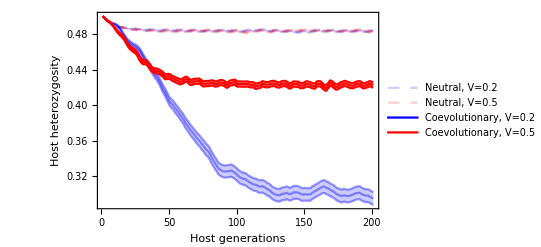

```mathematica
g2Legend=Legended[g2,leg3]
```

```mathematica
Export["/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/IslandMainland_Discrete_Specificity.png",g1Legend,"PNG",ImageResolution-> 300]
Export["/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/IslandMainland_Discrete_Virulence.png",g2Legend,"PNG",ImageResolution-> 300]
```

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/IslandMainland_Discrete_Specificity.png

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/IslandMainland_Discrete_Virulence.png

```mathematica
leg=LineLegend[{Directive[Orange,Opacity[0.3]],Directive[Red,Opacity[0.3]],Directive[Blue,Opacity[0.3]],Directive[Orange],Directive[Red],Directive[Blue]},{"Neutral, m_i=0.001","Neutral, m_i=0.01","Neutral, m_i=0.05","Coevolutionary, m_i=0.001","Coevolutionary, m_i=0.01","Coevolutionary, m_i=0.05"}];
```

```mathematica
g=Show[ListLinePlot[{mean[parsN],mean[parsN]+(2SD[parsN])/Sqrt[2000],mean[parsN]-(2SD[parsN])/Sqrt[2000]},PlotStyle->Directive[Blue,Opacity[0.2],Dashed],Filling->{2->{{3},{Directive[Blue,Opacity[0.1]]}}}],
ListLinePlot[{mean[parsN4],mean[parsN4]+(2SD[parsN4])/Sqrt[2000],mean[parsN4]-(2SD[parsN4])/Sqrt[2000]},PlotStyle->Directive[Red,Opacity[0.2],Dashed],Filling->{2->{{3},{Directive[Red,Opacity[0.1]]}}}],
ListLinePlot[{mean[parsN5],mean[parsN5]+(2SD[parsN5])/Sqrt[2000],mean[parsN5]-(2SD[parsN5])/Sqrt[2000]},PlotStyle->Directive[Orange,Opacity[0.2],Dashed],Filling->{2->{{3},{Directive[Orange,Opacity[0.1]]}}}],
ListLinePlot[{mean[pars1],mean[pars1]+(2SD[pars1])/Sqrt[2000],mean[pars1]-(2SD[pars1])/Sqrt[2000]},PlotStyle->Directive[Blue],Filling->{2->{{3},{Directive[Blue,Opacity[0.2]]}}}],
ListLinePlot[{mean[pars4],mean[pars4]+(2SD[pars4])/Sqrt[2000],mean[pars4]-(2SD[pars4])/Sqrt[2000]},PlotStyle->Directive[Red],Filling->{2->{{3},{Directive[Red,Opacity[0.2]]}}}],ListLinePlot[{mean[pars5],mean[pars5]+(2SD[pars5])/Sqrt[2000],mean[pars5]-(2SD[pars5])/Sqrt[2000]},PlotStyle->Directive[Orange],Filling->{2->{{3},{Directive[Orange,Opacity[0.2]]}}}],
PlotRange-> {0,0.5},Frame->True,FrameLabel-> {"Host generations","Host heterozygosity"},Axes-> False];
```

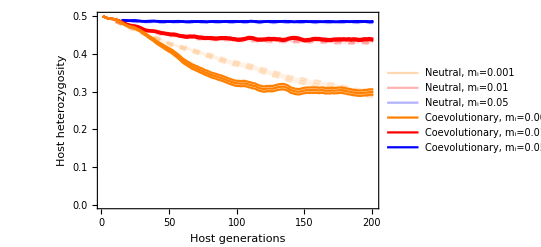

```mathematica
gLegend=Legended[g,leg]
```

```mathematica
Export["/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/IslandMainland_Discrete_Migration.png",gLegend,"PNG",ImageResolution-> 300]
```

/Users/madeline/Desktop/Mideo.lab2/Coevolution/Data sets/FIgures/IslandMainland_Discrete_Migration.png

```mathematica
parsN
parsN4
parsN5
```

{S→0,V→0.2,mH→0.05,mP→0.05,κH→300,κP→300,tMax→200}

{S→0,V→0.2,mH→0.01,mP→0.01,κH→300,κP→300,tMax→200}

{S→0,V→0.2,mH→0.001,mP→0.001,κH→300,κP→300,tMax→200}

```mathematica
pars5
```

{S→0.8,V→0.2,a→0.1,mH→0.001,mP→0.001,κH→300,κP→300,tMax→200}